## Introduction

Code used in paper  XXX

## Main

### Dynamic simulation

```mathematica
(*Preamble*)
{dt,n,T}={0.5,100,400}; 
{J,k,b,e}={1,-1,0.1,0};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
```

### Static simulation

#### Simulation

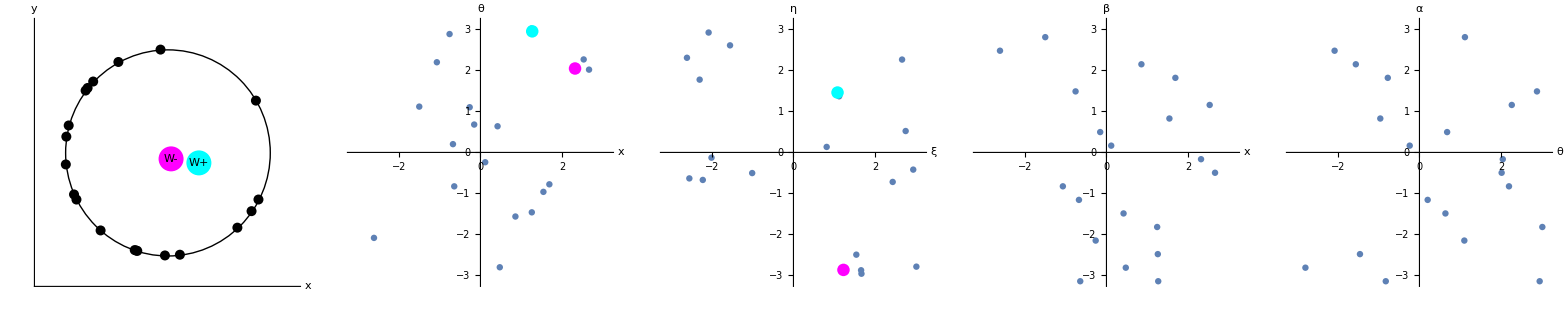

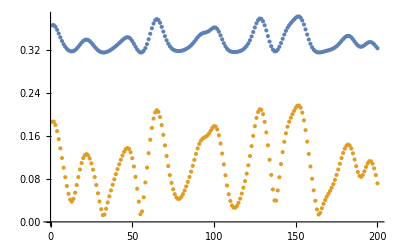

```mathematica
(*Preamble*)
{dt,n,T}={0.5,20,100}; 
{J,k,b,e}={1,-1,0,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
]
results=plotResults[znew,pin]
ListPlot[{Wp,Wm}//Abs]
```

```mathematica
ListPlot[{Wp,Wm}//Abs]
```

-Graphics-

#### Plots

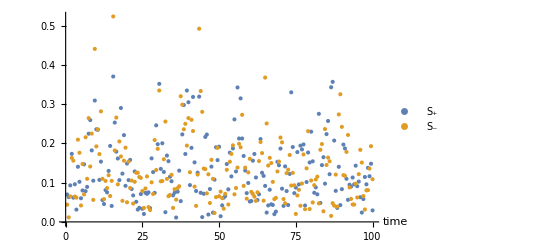

```mathematica
ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"S_+","S_-"}]
```

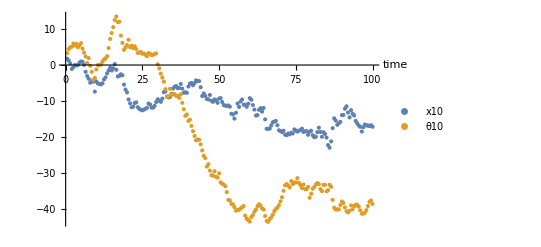

```mathematica
swarmalatorIndex=10;
ListPlot[{{ts,xs[[All,swarmalatorIndex]]}ᵀ,{ts,θs[[All,swarmalatorIndex]]}ᵀ},AxesLabel->{Style["time",13]},
PlotLegends->{"x"<>ToString[swarmalatorIndex],"θ"<>ToString[swarmalatorIndex]}]
```

```mathematica
(*Manipulate[ListPlot[{xs[[t,All]]//mod,θs[[t,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}],{t,1,Dimensions[xs][[2]],1}]*)
```

## Catalog states: E = 0

### Pure sync

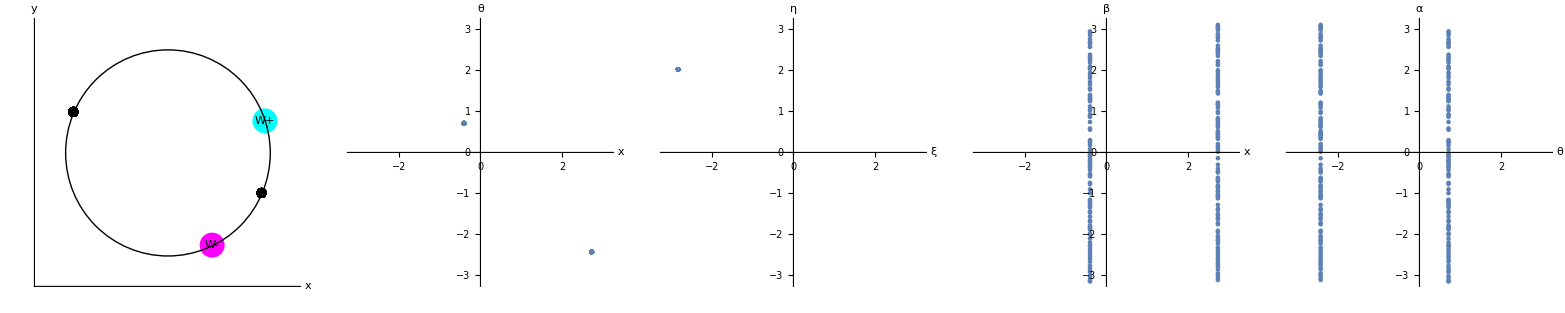

```mathematica
(*Preamble*)
{dt,n,T}={0.25,200,50}; 
{J,k}={1,2};

{Ex,Eθ} = {0,0};
b=0;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Partial sync

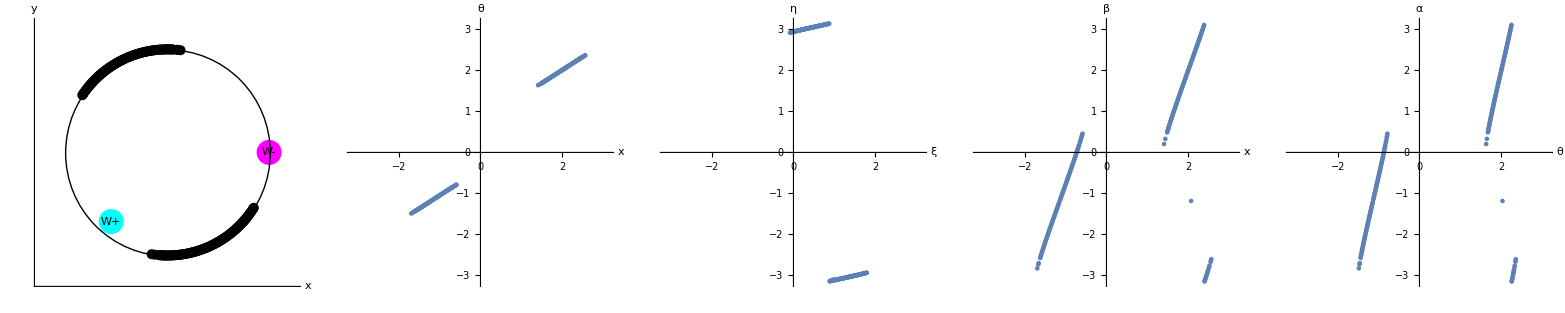

```mathematica
(*Preamble*)
{dt,n,T}={0.25,200,100}; 
{J,k}={1,2};

{Ex,Eθ} = {0,0};
b=0.5;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Double phase wave

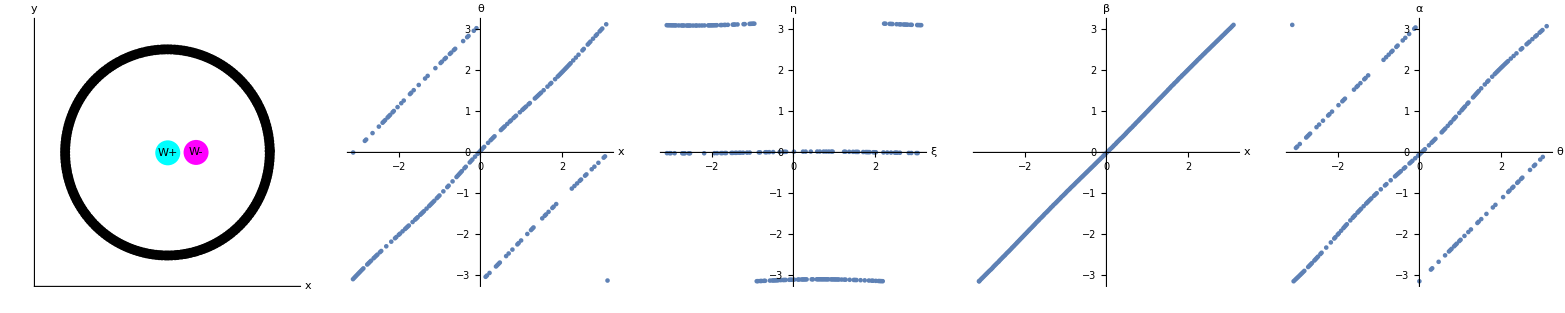

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,200}; 
(*{J,k}={1,1}; *)  (*Static sync / π state, depending on IC*)
(*{J,k}={1,-0.5};*) (*Static phase wave*)
(*{J,k}={1,-1.05};*) (*Active async*)
(*{J,k}={1,-3};*) (*Static async*)
{J,k}={1,-2};

{Ex,Eθ} = {0,0};
b=0.3;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Phase wave

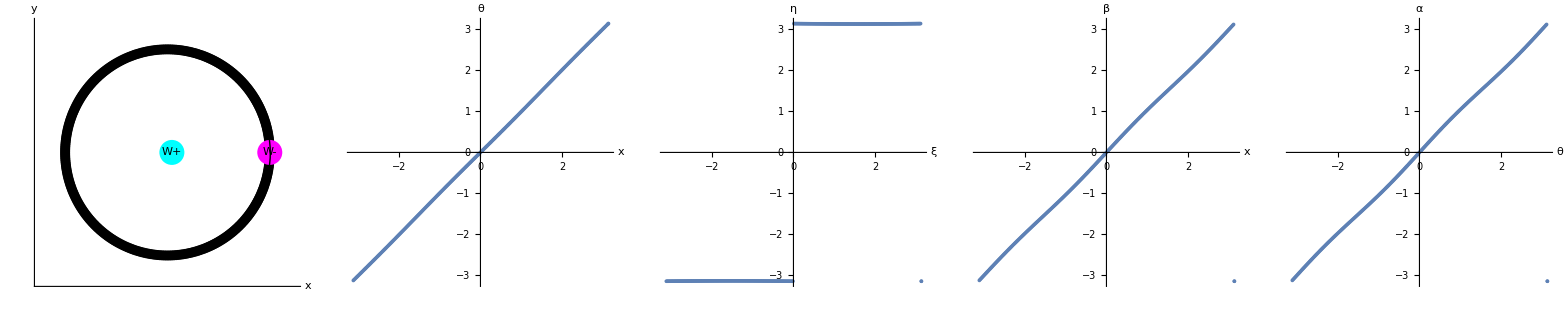

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={0,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

## Catalog states: E > 0

### Traveling loops

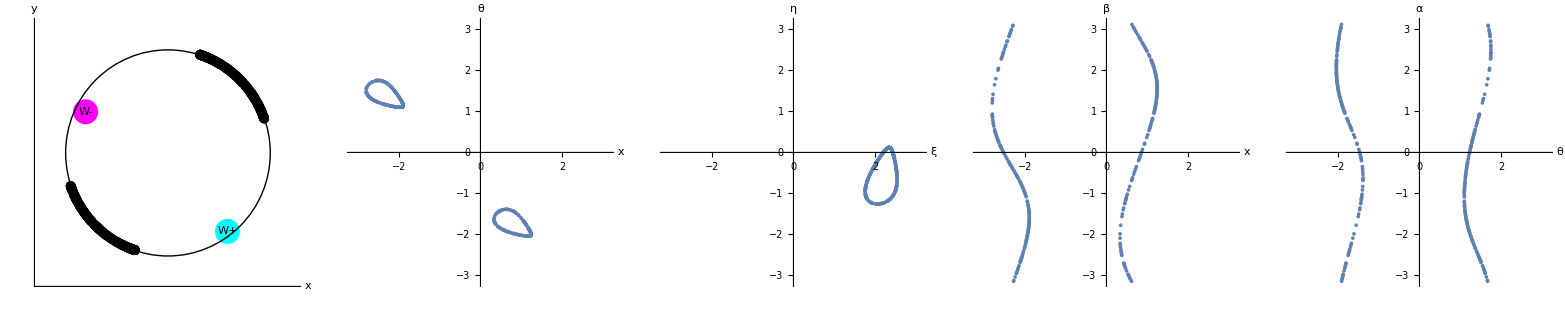

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={1.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Traveling horse shoes (broken loops)

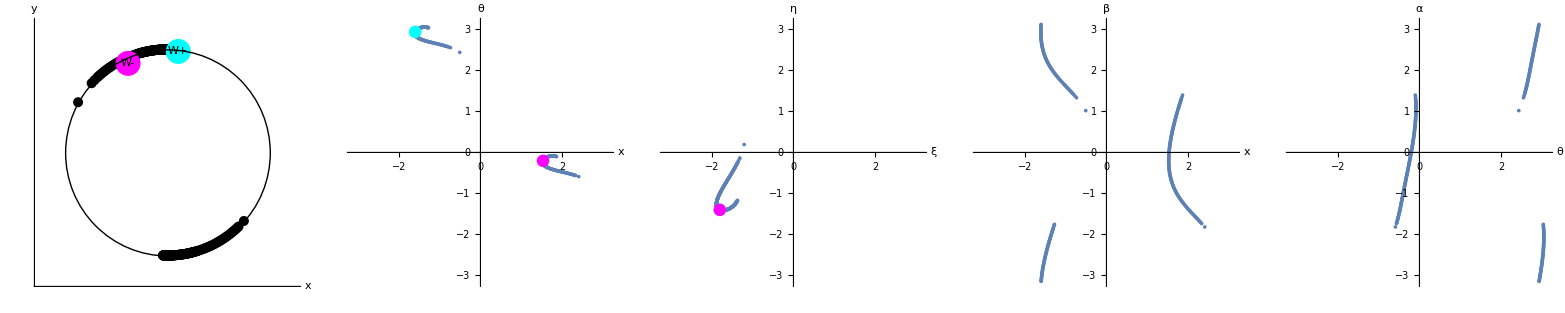

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={0.5,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;


{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Non-traveling loops

1. Here the loops dont travel

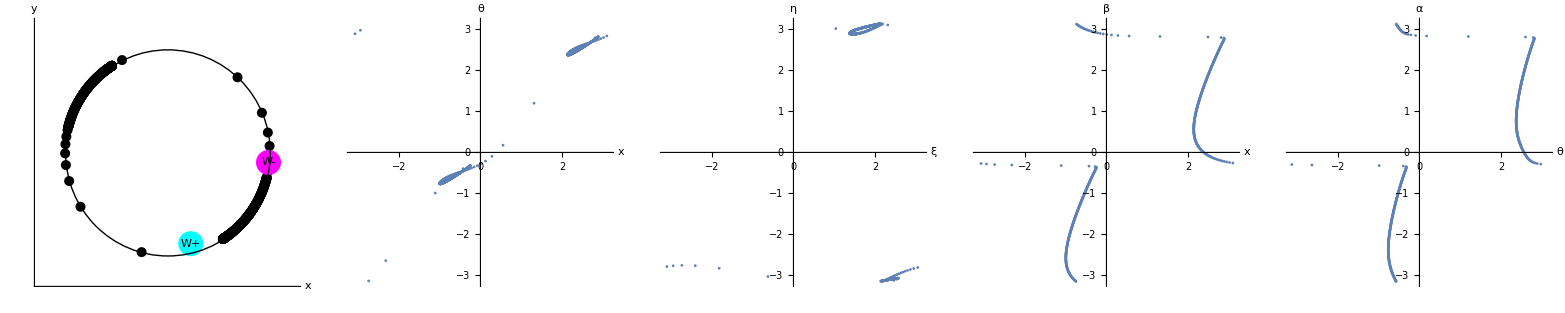

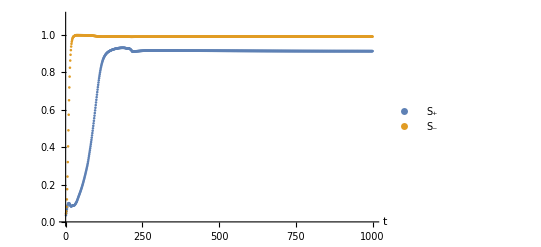

```mathematica
(*Preamble*)
{dt,n,T}={0.2,500,200}; 
{J,k}={1,2};
{e,b}={0.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{WpTemp,WmTemp}=findWs[znew];
AppendTo[Wp,WpTemp];AppendTo[Wm,WmTemp];
]
plotResults[znew,pin]

ListPlot[{Abs[Wp],Abs[Wm]},AxesLabel->{"t"},PlotLegends->{"S_+","S_-"},PlotRange->{0,1.1}]
```

### Messy waves

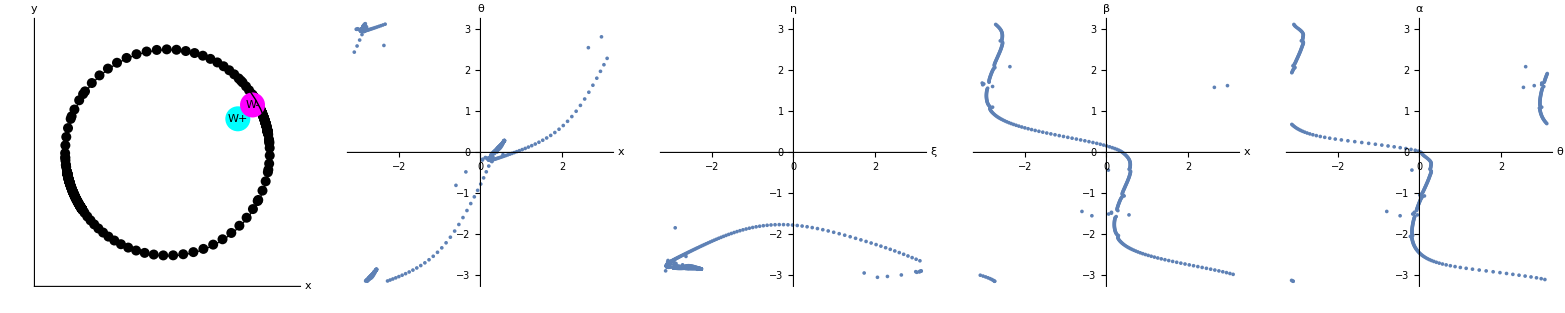

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={2.2,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Sliding phase waves -- further investigate here

The transients look a bit like a chimera here -- so watch in movie.

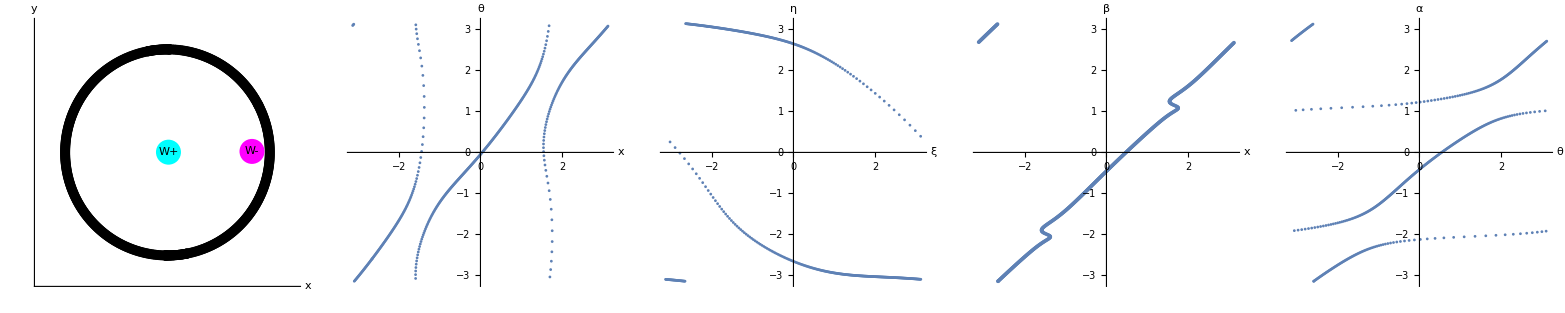

```mathematica
(*Preamble*)
{dt,n,T}={0.5,500,500}; 
{J,k}={1,-5};
{e,b}={0.9,2};
{xs,θs}={{},{}};
{Wp,Wm}={{},{}};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{x,θ}={znew[[1,All]],znew[[2,All]]};AppendTo[xs,x];AppendTo[θs,θ];
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
]
plotResults[znew,pin]
```

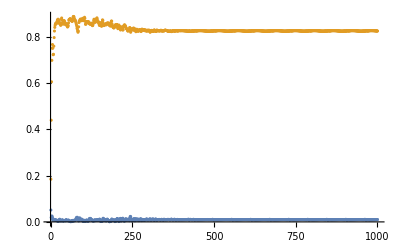

```mathematica
ListPlot[{Wp,Wm}//Abs]
```

```mathematica
Manipulate[ListPlot[{xs[[All,index]]//mod,θs[[All,index]]//mod},AxesLabel->{"t"},PlotLegends->{"x","θ"},PlotRange->{-π,π}],{index,1,n,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
{x,θ}={znew[[1,All]],znew[[2,All]]};
```

### Noisy phase wave

Here the wave in (x,β) space breathes

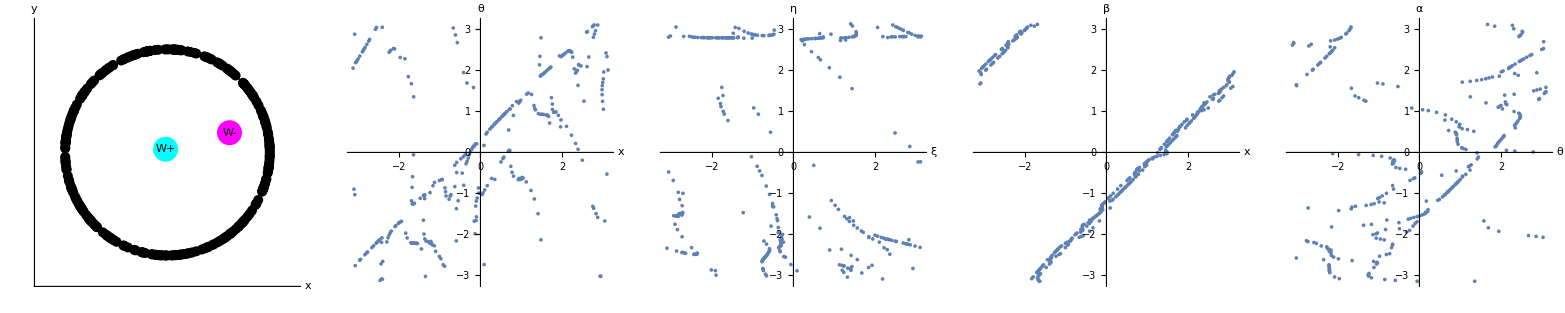

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{e,b}={1.9,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Bursty async

Here the wave in (x,β) space bursts and rotates.

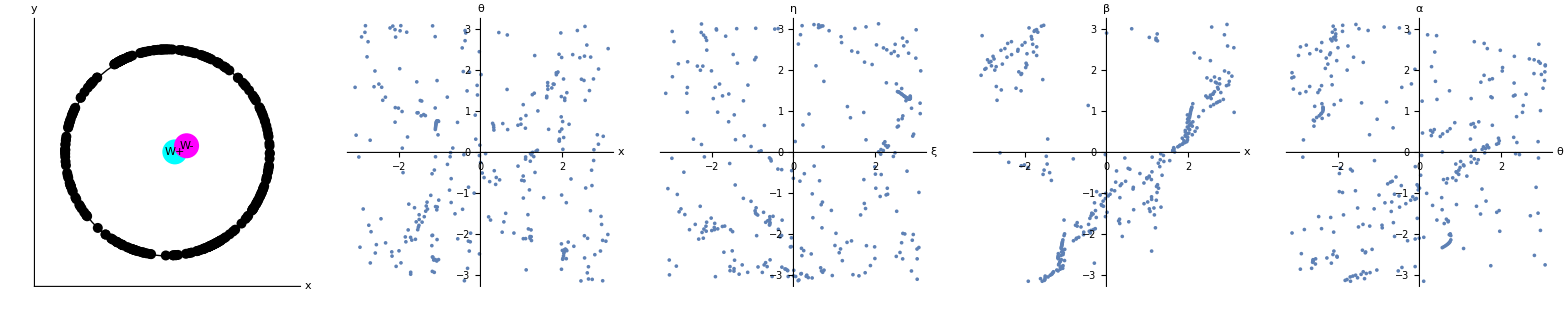

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{e,b}={2.5,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Non-traveling loops

1. Here the loops dont travel

```mathematica
(*Preamble*)
{dt,n,T}={0.2,500,200}; 
{J,k}={1,2};
{e,b}={0.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{WpTemp,WmTemp}=findWs[znew];
AppendTo[Wp,WpTemp];AppendTo[Wm,WmTemp];
]
plotResults[znew,pin]

ListPlot[{Abs[Wp],Abs[Wm]},AxesLabel->{"t"},PlotLegends->{"S_+","S_-"},PlotRange->{0,1.1}]
```

-Graphics-

-Graphics-

## S(K): E = 0

### b = 0

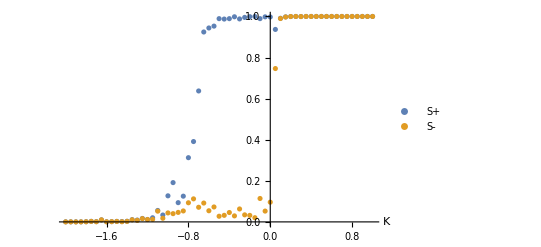

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,50}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-2,1,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### b = 0.1

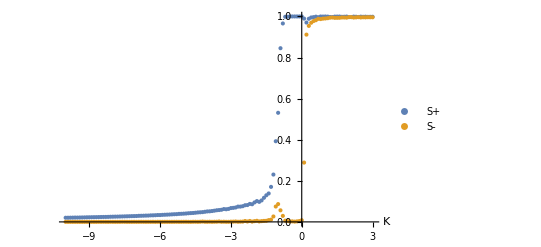

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,100}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0.1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,3,0.1}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### b = 0.2

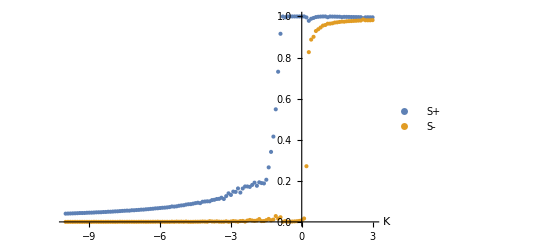

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,100}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0.2;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,3,0.1}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

## S(b): E = 0

### K = 2

```mathematica
data1=ParallelTable[
{dt,n,T}={0.5,200,200}; 
{J,k}={1,2};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-1.5,1.5,0.025}
];
```

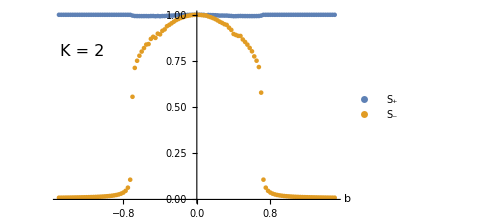

figures/order-pars-versus-b-K2.png

```mathematica
p1=ListPlot[{data1[[All,{1,2}]],data1[[All,{1,3}]]},AxesLabel->{Style["b",25,Italic]},PlotLegends->{Style["S_+",17,Italic],Style["S_-",17,Italic]},AxesStyle->15,Epilog->{Text[Style["K = 2",16,Italic],{-1.25,0.8}]},ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-versus-b-K2.png",p1]
```

### K = -0.5

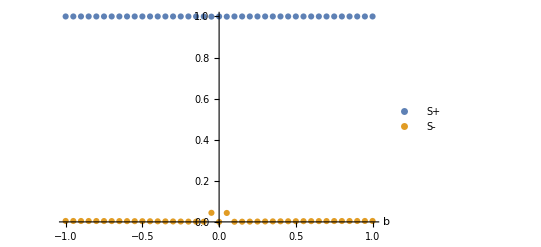

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,200}; 
{J,k}={1,-0.5};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-1,1,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"b"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### K = -5

```mathematica
data2=ParallelTable[
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.8Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-5,5,0.025}
];
```

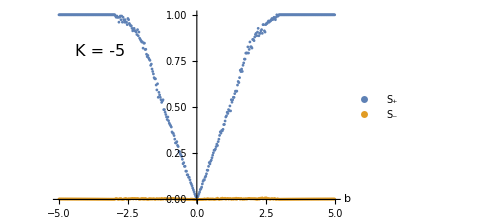

```mathematica
p2=ListPlot[{data2[[All,{1,2}]],data2[[All,{1,3}]]},AxesLabel->{Style["b",25,Italic]},PlotLegends->{Style["S_+",17,Italic],Style["S_-",17,Italic]},AxesStyle->15,Epilog->{Text[Style["K = -5",16,Italic],{-3.5,0.8}]},ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-versus-b-Km5.png",p2];
```

### Plot together

```mathematica
pAll=Grid[{{p1,p2}}]
Export["figures/order-pars-together.png",pAll];
```

-Graphics- | -Graphics-

## Bistability -- is there hysteresis here?

### S(b)

Result: don’t seem to find any

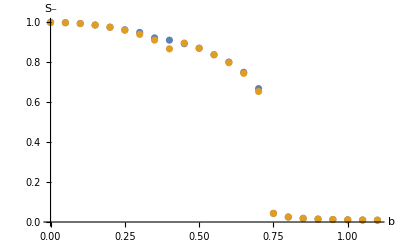

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
data1=ParallelTable[
{dt,n,T}={0.25,300,500};
{J,k}={1,2};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,0,1.1,0.05}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={0.25,300,500};
{J,k}={1,2};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,0,1.1,0.05}
];

ListPlot[{data1[[All,{1,3}]],data2[[All,{1,3}]]},AxesLabel->{Style["b",15,Italic],Style["S_-",15,Italic]},LabelStyle->15]
```

Hmm, dont see any.

### S(E)

#### (J,K,b) = (1,2,0.5) -- sync --> traveling loops --> no hysteresis

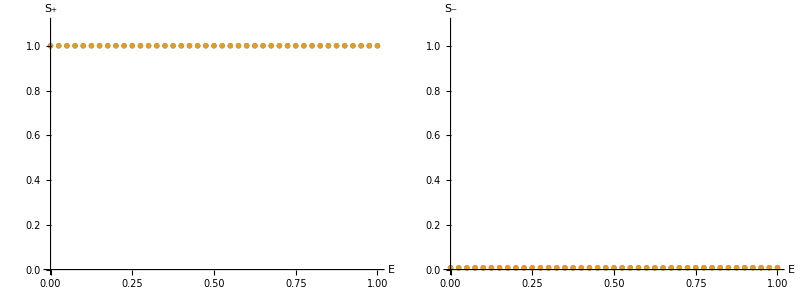

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
data1=ParallelTable[
{dt,n,T}={0.25,200,300};
{J,k,b}={1,2,0.5};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,0,1,0.025}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={0.25,200,300};
{J,k,b}={1,2,0.5};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,0,1,0.025}
];

p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium];
p2=ListPlot[{data1[[All,{1,3}]],data2[[All,{1,3}]]},AxesLabel->{Style["E",15,Italic],Style["S_-",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium];
Grid[{{p1,p2}}]
```

#### (J,K,b) = (1,-5,0.5) -- hysteresis

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

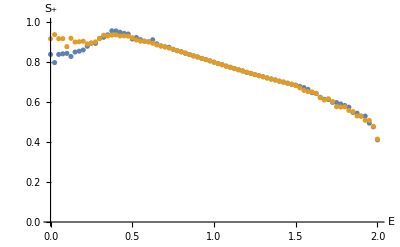

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{dt1,n1,T1}={0.5,100,200};
{emin,emax,de}={0,2,0.025};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1},LabelStyle->{"J,K,b = 1,-5,2"}]
```

So there is hysteresis in the early regime --> static phase wave. Is this a finite N effect?

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

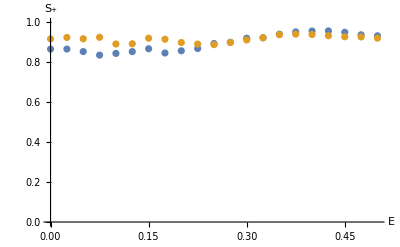

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{dt1,n1,T1}={0.5,300,200};
{emin,emax,de}={0,0.5,0.025};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1},LabelStyle->{"J,K,b = 1,-5,2"}]
```

These are differences in the static phase wave.

#### (J,K,b) = (1,2,2) -- static phase wave --> messy loop. Hystersis.

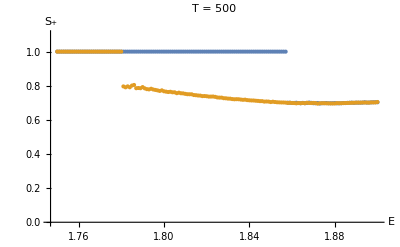

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{j1,k1,b1}={1,2,2};
{dt1,n1,T1}={0.5,200,500};
{emin,emax,de}={1.75,1.9,0.001};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},LabelStyle->{"J,K,b = 1,-5,2"},PlotLabel->"T = "<>ToString[T1]]
```

Retest for larger T -- may be spurious long transient.

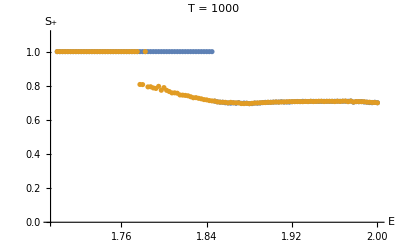

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{j1,k1,b1}={1,2,2};
{dt1,n1,T1}={0.5,100,1000};
{emin,emax,de}={1.7,2,0.0025};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},LabelStyle->{"J,K,b = 1,-5,2"},PlotLabel->"T = "<>ToString[T1]]
```

#### Plot for figure

```mathematica
data1={{1.75,0.9999967703560034,0.017783146957279502},{1.751,0.999996735228741,0.017866416051130433},{1.752,0.9999966993655168,0.017950993791028377},{1.753,0.9999966627441955,0.01803691179467883},{1.754,0.9999966253417754,0.018124202714377424},{1.755,0.9999965871343521,0.01821290027988402},{1.756,0.9999965480970666,0.018303039343491503},{1.757,0.9999965082040636,0.018394655927375204},{1.758,0.9999964674284408,0.018487787273382093},{1.759,0.9999964257421966,0.018582471895377695},{1.76,0.9999963831161758,0.01867874963436841},{1.761,0.9999963395200097,0.018776661716479993},{1.762,0.9999962949220544,0.0188762508140687},{1.763,0.9999962492893252,0.018977561110083672},{1.764,0.9999962025874253,0.01908063836593499},{1.765,0.9999961547804729,0.019185529993075857},{1.766,0.9999961058310227,0.0192922851285374},{1.767,0.9999960556999782,0.01940095471468086},{1.768,0.9999960043465064,0.019511591583447504},{1.769,0.9999959517279375,0.019624250545406924},{1.77,0.9999958977996717,0.019738988483901834},{1.771,0.9999958425150612,0.019855864454712907},{1.772,0.9999957858253021,0.019974939791509216},{1.773,0.999995727679305,0.020096278217596904},{1.774,0.9999956680235695,0.020219945964337512},{1.775,0.999995606802042,0.020346011896763983},{1.776,0.999995543955959,0.020474547646846673},{1.777,0.9999954794236948,0.020605627755042533},{1.778,0.9999954131405826,0.020739329820680795},{1.779,0.999995345038734,0.02087573466187027},{1.78,0.999995275046836,0.021014926485626303},{1.781,0.999995203089942,0.02115699306901676},{1.782,0.99999512908924,0.021302025952177225},{1.783,0.9999950529618092,0.02145012064408865},{1.784,0.9999949746203523,0.0216013768421598},{1.785,0.9999948939729115,0.021755898666733182},{1.786,0.9999948109225631,0.021913794911644992},{1.787,0.9999947253670795,0.02207517931225814},{1.788,0.9999946371985791,0.02224017083236026},{1.789,0.9999945463031298,0.02240889397149496},{1.79,0.9999944525603375,0.022581479094541192},{1.791,0.9999943558428878,0.02275806278541215},{1.792,0.9999942560160566,0.022938788226980183},{1.793,0.9999941529371701,0.023123805609591146},{1.794,0.9999940464550309,0.023313272570767693},{1.795,0.9999939364092835,0.02350735466885101},{1.796,0.9999938226297241,0.023706225893871835},{1.797,0.9999937049355563,0.023910069219031146},{1.798,0.9999935831345688,0.02411907719678125},{1.799,0.99999345702224,0.024333452603764738},{1.8,0.999993326380766,0.02455340913945659},{1.801,0.9999931909779799,0.024779172183917536},{1.802,0.9999930505661803,0.025010979620688316},{1.803,0.9999929048808366,0.02524908273150519},{1.804,0.9999927536391698,0.02549374717050766},{1.805,0.9999925965385777,0.02574525402643842},{1.806,0.9999924332549144,0.026003900982393937},{1.807,0.9999922634405707,0.02627000358407434},{1.808,0.9999920867223581,0.02654389662872217},{1.809,0.9999919026991625,0.026825935688808318},{1.81,0.9999917109393293,0.027116498786188103},{1.811,0.9999915109777614,0.027415988234986487},{1.812,0.9999913023126789,0.027724832673701384},{1.813,0.9999910844019876,0.0280434893103705},{1.814,0.9999908566592344,0.028372446407975174},{1.815,0.9999906184490431,0.028712226041507072},{1.816,0.9999903690819949,0.029063387163013092},{1.817,0.9999901078088496,0.02942652901677169},{1.818,0.9999898338140133,0.02980229495371014},{1.819,0.9999895462081345,0.030191376702291755},{1.82,0.9999892440196889,0.030594519163224435},{1.821,0.9999889261853854,0.031012525807088354},{1.822,0.9999885915392046,0.031446264768499606},{1.823,0.9999882387998137,0.03189667574805182},{1.824,0.9999878665560964,0.03236477785448486},{1.825,0.9999874732504362,0.032851678546340864},{1.826,0.9999870571593334,0.03335858386460498},{1.827,0.9999866163708537,0.03388681018869953},{1.828,0.9999861487582661,0.03443779779911481},{1.829,0.9999856519490874,0.035013126593955404},{1.8299999999999998,0.9999851232885711,0.03561453438878932},{1.831,0.9999845597964019,0.03624393833340911},{1.8319999999999999,0.9999839581150617,0.0369034601149434},{1.833,0.9999833144478896,0.03759545579307865},{1.8339999999999999,0.9999826244842995,0.03832255134634575},{1.835,0.9999818833088817,0.039087685318504053},{1.8359999999999999,0.9999810852900439,0.03989416037264201},{1.837,0.999980223942486,0.04074570613165265},{1.838,0.9999792917558237,0.0416465564745247},{1.839,0.9999782799788736,0.04260154556895583},{1.84,0.9999771783451822,0.04361622850836292},{1.841,0.9999759747194751,0.04469703473135839},{1.842,0.9999746546360532,0.04585146583139673},{1.843,0.9999732006868045,0.047088354573752156},{1.844,0.999971591695669,0.04841821005059951},{1.845,0.9999698015827925,0.04985368691276231},{1.846,0.9999677977656356,0.05141023816127521},{1.847,0.999965538847576,0.0531070480407671},{1.8479999999999999,0.9999629711696655,0.054968408182074165},{1.849,0.999960023468496,0.05702582628380925},{1.8499999999999999,0.9999565982088297,0.059321410858377874},{1.851,0.9999525566835769,0.06191362937097804},{1.8519999999999999,0.9999476914096047,0.06488786751212315},{1.853,0.9999416695695695,0.0683778465947435},{1.8539999999999999,0.9999338990491173,0.0726158551811151},{1.855,0.9999231297993569,0.07808063749866523},{1.856,0.9999055973974817,0.08617752794133722},{1.857,0.9997922113137521,0.12453868946044104},{1.858,0.700600166910035,0.6783961875706164},{1.859,0.7003704808160222,0.680175411859274},{1.86,0.6990918830025903,0.6803080236284249},{1.861,0.6992667804464867,0.6811257036013373},{1.862,0.7004488954140857,0.6833187866085147},{1.863,0.6988283826911879,0.6835472291371159},{1.864,0.6972550930362663,0.6825801788695453},{1.865,0.6995514737019967,0.6870811257074037},{1.8659999999999999,0.6977307313982466,0.6862109547217158},{1.867,0.6986980348762509,0.6880564691161825},{1.8679999999999999,0.7015003309362268,0.6900400583298643},{1.869,0.6997858450378939,0.6894974742221471},{1.8699999999999999,0.6975728859510392,0.6904324560141112},{1.871,0.6973965547173899,0.6907180172608731},{1.8719999999999999,0.6988433262449038,0.6922864922258153},{1.873,0.6957169010562565,0.690164109705989},{1.874,0.6976972992149583,0.6928161538767821},{1.875,0.6974834758768775,0.6936477262589389},{1.8760000000000001,0.6987131472204507,0.6941814424541359},{1.877,0.6972594567974619,0.6948947164215519},{1.8780000000000001,0.6975639770231807,0.6963689577283431},{1.879,0.6976070100112292,0.6959050058000046},{1.8800000000000001,0.6984875487280076,0.696507419766349},{1.881,0.6969749083089591,0.6965955128081139},{1.8820000000000001,0.6970716742516795,0.6959948896654818},{1.883,0.6973815706957271,0.6965353441923435},{1.884,0.6987932021976704,0.6959510115347854},{1.885,0.6984541590992992,0.6971109083570712},{1.886,0.6997218632356033,0.6964139817647003},{1.887,0.7002400326373465,0.6955002301948773},{1.888,0.7009161605740736,0.6959671377810068},{1.889,0.6997407247002809,0.6944962442844743},{1.89,0.701028324375683,0.6949753154979185},{1.891,0.7004722693279667,0.6948614868224497},{1.892,0.7009899695428828,0.6941497697810862},{1.8929999999999998,0.700954614590927,0.6957020937296401},{1.894,0.7031794740156597,0.6962492152476808},{1.8949999999999998,0.7011233415811378,0.6927526638547417},{1.896,0.7016751836592097,0.6932882442186048},{1.8969999999999998,0.7022835346001339,0.6952080312266412},{1.898,0.7030736083641045,0.6965583574876809},{1.8989999999999998,0.7032506510898515,0.6966976218980526},{1.9,0.7029857788083771,0.6965114835047813}};

data2={{1.75,0.9999967703560034,0.017783146957279432},{1.751,0.999996735228741,0.017866416051132233},{1.752,0.9999966993655168,0.01795099379102754},{1.753,0.9999966627441955,0.018036911794679984},{1.754,0.9999966253417754,0.018124202714379572},{1.755,0.9999965871343521,0.01821290027988541},{1.756,0.9999965480970666,0.01830303934349344},{1.757,0.9999965082040636,0.018394655927377476},{1.758,0.9999964674284408,0.018487787273381594},{1.759,0.9999964257421966,0.018582471895378785},{1.76,0.9999963831161758,0.018678749634368077},{1.761,0.9999963395200097,0.018776661716480885},{1.762,0.9999962949220544,0.018876250814069594},{1.763,0.9999962492893252,0.018977561110084695},{1.764,0.9999962025874253,0.01908063836593658},{1.765,0.9999961547804729,0.019185529993078095},{1.766,0.9999961058310227,0.019292285128539397},{1.767,0.9999960556999782,0.01940095471468276},{1.768,0.9999960043465064,0.0195115915834503},{1.769,0.9999959517279375,0.01962425054540674},{1.77,0.9999958977996717,0.019738988483904308},{1.771,0.9999958425150612,0.019855864454716127},{1.772,0.9999957858253021,0.019974939791512176},{1.773,0.999995727679305,0.020096278217598493},{1.774,0.9999956680235695,0.02021994596434072},{1.775,0.999995606802042,0.020346011896765777},{1.776,0.999995543955959,0.020474547646846853},{1.777,0.9999954794236948,0.020605627755042624},{1.778,0.9999954131405826,0.020739329820682453},{1.779,0.999995345038734,0.020875734661871606},{1.78,0.999995275046836,0.021014926485627222},{1.781,0.796131733683242,0.6259072943826792},{1.782,0.7907183632515176,0.6295623389195948},{1.783,0.7963937562538019,0.6260258806545235},{1.784,0.7908970625705467,0.625239675889099},{1.785,0.8009899580272606,0.6197347989189905},{1.786,0.8046299009679494,0.6188458815654616},{1.787,0.7855124492595157,0.631489773709782},{1.788,0.786722935866399,0.6322500327904413},{1.789,0.785499845411327,0.6296012023266038},{1.79,0.7921713226251093,0.6202909096017196},{1.791,0.7846059385872663,0.6294717813483793},{1.792,0.780070979088705,0.6361330553022502},{1.793,0.7786117122507362,0.639301038298132},{1.794,0.7824181546965403,0.6354717518076776},{1.795,0.7779409974966063,0.6313827642402059},{1.796,0.77543383872627,0.635635596551679},{1.797,0.7728011074918313,0.6353713358404044},{1.798,0.7696035443299931,0.634752335224753},{1.799,0.7731162714138646,0.6321758367433253},{1.8,0.767514602304282,0.6396221249652609},{1.801,0.7653200119432881,0.6411734354999357},{1.802,0.7632600249040137,0.6408327273399759},{1.803,0.7647503429062139,0.6374902655569404},{1.804,0.7616082775980977,0.6363908646855418},{1.805,0.7615753943292791,0.6387784444523713},{1.806,0.7563871898277736,0.6426751246465968},{1.807,0.7594122008250006,0.6438018525851085},{1.808,0.7558061231870108,0.641711615297188},{1.809,0.7551554667663474,0.6434884599953201},{1.81,0.7524479168863035,0.6455261520105701},{1.811,0.7503545629752579,0.6436701616963395},{1.812,0.7500510784447556,0.6451333755892044},{1.813,0.7498114257239246,0.6489306679345439},{1.814,0.7454305150426837,0.6461790506382461},{1.815,0.7444435101290638,0.64449190589861},{1.816,0.7427537283733388,0.6510604112823764},{1.817,0.7422461094415618,0.6465988918596299},{1.818,0.7391399314122201,0.6513948241301579},{1.819,0.7396275373026024,0.6455904303867913},{1.82,0.7384886628341512,0.6518962316698161},{1.821,0.736344946963108,0.6510110986894646},{1.822,0.7364421797984734,0.6498593959552023},{1.823,0.7368452723385175,0.6508050226441618},{1.824,0.7348643748290997,0.6496873365257491},{1.825,0.7313698029508624,0.651943692883856},{1.826,0.7304371968810366,0.6540447771193847},{1.827,0.7303611512659057,0.6509631817707785},{1.828,0.7269209749000745,0.6543805833733746},{1.829,0.7263533031447474,0.6560212919315097},{1.8299999999999998,0.7246092991874122,0.6574530905484963},{1.831,0.7242964813739078,0.6562285850920897},{1.8319999999999999,0.7218310306252536,0.6539343257407232},{1.833,0.7205833948605324,0.6552152028230467},{1.8339999999999999,0.7212339303226527,0.6561809734288414},{1.835,0.7207615813603314,0.6595240614363286},{1.8359999999999999,0.7190334170544919,0.6602197518115468},{1.837,0.7175926399024688,0.6589894089508691},{1.838,0.7184859926336868,0.6617549057962246},{1.839,0.7157687410100046,0.6631588180064731},{1.84,0.7145612926847047,0.6613692828238518},{1.841,0.7137176733786493,0.6618318814235413},{1.842,0.7135447533690485,0.6661248504093336},{1.843,0.7121667096921358,0.6650927379370386},{1.844,0.711227064470508,0.6657297883318422},{1.845,0.7097364193623262,0.6661973041266807},{1.846,0.7097172480781933,0.6672697210118774},{1.847,0.7069750084431468,0.6665676769252776},{1.8479999999999999,0.7077791931626015,0.6696573925981218},{1.849,0.7071258299682671,0.6711084135646644},{1.8499999999999999,0.7043839201838642,0.6700044756929558},{1.851,0.7064291989332665,0.673803328971293},{1.8519999999999999,0.7045842138149631,0.6743582930317195},{1.853,0.7030797589240209,0.6741245372222874},{1.8539999999999999,0.7025499465058066,0.6746119686463351},{1.855,0.7019840707596123,0.6745924785002662},{1.856,0.7019553779098581,0.6761103726739994},{1.857,0.7011802206254131,0.6769885091276401},{1.858,0.6994348225351836,0.6764968178678088},{1.859,0.7003903220152952,0.6783188542283018},{1.86,0.6989125033408323,0.6805479470180127},{1.861,0.6984909653276838,0.6804843681096306},{1.862,0.6968183370190959,0.6806202734881559},{1.863,0.6984967176311196,0.6824014285451547},{1.864,0.697685826179568,0.6841193708388663},{1.865,0.6987998481276266,0.6862866704198881},{1.8659999999999999,0.6975571816377476,0.6865522949914632},{1.867,0.7005869319116307,0.689343387293942},{1.8679999999999999,0.6988994571553256,0.6889258225762603},{1.869,0.6985811272108476,0.6899503007854055},{1.8699999999999999,0.6993006786990618,0.6913512455829433},{1.871,0.6983146024963429,0.6917086449253904},{1.8719999999999999,0.6949629089579578,0.6899522085139893},{1.873,0.6973828916030406,0.6929996202564751},{1.874,0.6974789474166598,0.69253900351582},{1.875,0.697889795969748,0.6941052254357918},{1.8760000000000001,0.6966771325057756,0.6940438308389634},{1.877,0.6968396639878147,0.694217928416875},{1.8780000000000001,0.6960881339010943,0.6948857202419826},{1.879,0.6960766366749102,0.6953908534307357},{1.8800000000000001,0.6958508398020871,0.695310110097459},{1.881,0.698162934973833,0.6978963173580327},{1.8820000000000001,0.697482684777254,0.6958673923818022},{1.883,0.6976445804257426,0.6959736037517452},{1.884,0.6980732396968254,0.6954359416113488},{1.885,0.6988151275605317,0.6966146192140423},{1.886,0.6989688119193632,0.6959280973962276},{1.887,0.6998715396802488,0.6982827373332234},{1.888,0.7002066341005134,0.6977643204805608},{1.889,0.7004549107637111,0.6980271090564973},{1.89,0.7009341098751737,0.6968074838573314},{1.891,0.7015216110286736,0.6981128922621924},{1.892,0.7008224314169045,0.6971163169688502},{1.8929999999999998,0.7017391720045255,0.6981045965959002},{1.894,0.7013845964869453,0.697170435691337},{1.8949999999999998,0.7017061993625686,0.6976352504784403},{1.896,0.7008671114752794,0.6964493540307206},{1.8969999999999998,0.7025197296085268,0.6972286812877757},{1.898,0.702163079244126,0.6955554290529422},{1.8989999999999998,0.7022702229382192,0.6946522761634903},{1.9,0.7048097377697218,0.6963799689083896}};
```

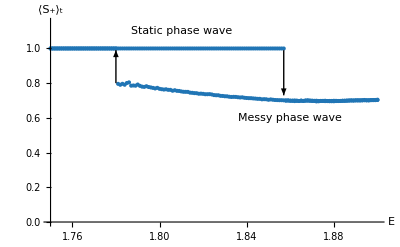

figures/hysteresis-static-phase-wave.png

```mathematica
{i1,i2}={1.78,1.857};
col=ColorData[index,"ColorList"];
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",17,Italic],Style["⟨S_+⟩_t",17,Italic]},LabelStyle->15,PlotRange->{{1.75,1.9},{0,1.15}},LabelStyle->{"J,K,b = 1,-5,2"},
PlotStyle->{col,col},
Epilog->{
{col,Arrow[{{i1,0.8},{i1,0.99}}]},
{col,Arrow[{{i2,0.99},{i2,0.73}}]},
Text[Style["Static phase wave",11],{1.81,1.1}],
Text[Style["Messy phase wave",11],{1.86,0.6}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/hysteresis-static-phase-wave.png",p1]
```

#### (J,K,b) = (1,-2,0.3) -- double phase wave --> noisy phase wave: no hysteresis

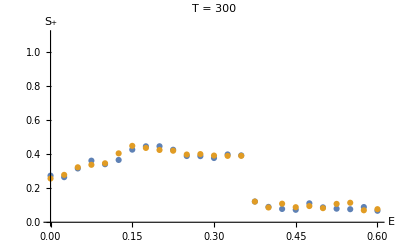

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{j1,k1,b1}={1,-2,0.3};
{dt1,n1,T1}={0.5,300,300};
{emin,emax,de}={0,0.6,0.025};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},LabelStyle->{"J,K,b = 1,-5,2"},PlotLabel->"T = "<>ToString[T1]]
```

Probably not the right order parameter...

#### (J,K,b) = (1,-5,2) -- double phase wave --> sliding phase wave: no hysteresis.

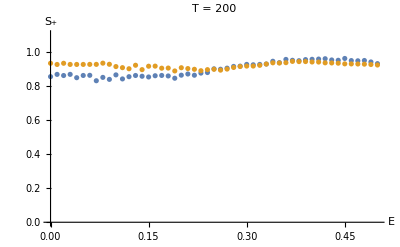

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
{j1,k1,b1}={1,-5,2};
{dt1,n1,T1}={0.5,300,200};
{emin,emax,de}={0,0.5,0.01};

data1=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

(*Start from sync: z_new = uniform on [1.99π, 2π]*)
data2=ParallelTable[
{dt,n,T}={dt1,n1,T1};
{J,k,b}={j1,k1,b1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{e,Sp,Sm},
{e,emin,emax,de}
];

ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",15,Italic],Style["S_+",15,Italic]},LabelStyle->15,PlotRange->{0,1.1},LabelStyle->{"J,K,b = 1,-5,2"},PlotLabel->"T = "<>ToString[T1]]
```

Probably not the right order parameter...

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```